# Higgs Exotic Decay

```mathematica
ClearAll["Global`*"]
```

## SM parameters

```mathematica
σggF=48.6;(*pb*)
σppH=55.1;(*pb*)
ΓSM=4.07*10^-3;(*GeV*)
mb=4.19;
mc=1.27;
mτ=1.78;
mμ=0.105;
ms=0.093;
mh=125.;
v=174.;
```

## Branching Ratio and Decay Rate

```mathematica
μBR[mS_]:=(mμ^2 Re[(mS^2-4 mμ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]+mμ^2 Re[(mS^2-4 mμ^2)^(3/2)]+3 ms^2 Re[(mS^2-4 ms^2)^(3/2)]);
τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
ghSS[mS_,sinθ_]:=2 √2 λ[mS,sinθ]v sinθ^2-√A2[mS,sinθ] sinθ;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mh)√(1-4 mS^2/mh^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
```

```mathematica
σggF*BRhSS[2,0.15]*μBR[2]^2
```

0.0000204792

## LHC result

```mathematica
dataset=Import[NotebookDirectory[]<>"LHC.csv"];
limit[mS_]:=Interpolation[dataset][mS]
```

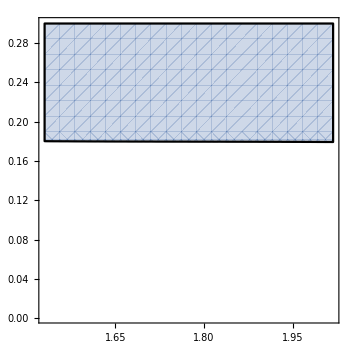

```mathematica
RegionPlot[σggF*BRhSS[mS,sinθ]*μBR[mS]^2≥10^-3 limit[mS],{mS,dataset[[1,1]],dataset[[-1,1]]},{sinθ,0.001,0.3}]
```